# NNPSS Summer school, Yale, 2018 Exercise I Sivers A_UT^sin[Φ_h-Φ_S]asymmetry Semi-Inclusive Deep Inelastic Scattering author: Alexei Prokudin email: prokudin@jlab.org

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/avp5627/GIT/nnpss-2018

```mathematica
<<wwsidis.m
```

Package WW-SIDIS contains the set of TMDs calculated with WW approximation and SIDIS structure functions

Copyright: Alexei Prokudin (PSU Berks), Kemal Tezgin (UConn), Version 1.01 (06/05/2018)

e-mail: prokudin@jlab.org, kemal.tezgin@uconn.edu

https://github.com/prokudin/WW-SIDIS

If you use this package, please, site arXiv for this paper and https://github.com/prokudin/WW-SIDIS

___________________________________________________________________________

Contains the following functions:

f1u[x_,Q2_ ] is the unpolarised collinear PDF for u quark, bibitem{Martin:2009iq}

f1d[x_,Q2_ ] is the unpolarised collinear PDF for d quark, bibitem{Martin:2009iq}

f1ubar[x_,Q2_ ] is the unpolarised collinear PDF for ubar quark, bibitem{Martin:2009iq}

f1dbar[x_,Q2_ ] is the unpolarised collinear PDF for dbar quark, bibitem{Martin:2009iq}

f1s[x_,Q2_ ] is the unpolarised collinear PDF for s quark, bibitem{Martin:2009iq}

f1sbar[x_,Q2_ ] is the unpolarised collinear PDF for sbar quark, bibitem{Martin:2009iq}

D1u[pion_, z_, Q2_ ] is the unpolarised collinear FF for u quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1d[pion_, z_, Q2_ ] is the unpolarised collinear FF for dbar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1ubar[pion_, z_, Q2_ ] is the unpolarised collinear FF for ubar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1dbar[pion_, z_, Q2_ ] is the unpolarised collinear FF for dbar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1s[pion_, z_, Q2_ ] is the unpolarised collinear FF for s quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1sbar[pion_, z_, Q2_ ] is the unpolarised collinear FF for sbar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

g1u[x_,Q2_ ] is the helicity collinear PDF for u quark, bibitem{Gluck:1998xa}

g1d[x_,Q2_ ] is the helicity collinear PDF for d quark, bibitem{Gluck:1998xa}

g1ubar[x_,Q2_ ] is the helicity collinear PDF for ubar quark, bibitem{Gluck:1998xa}

g1dbar[x_,Q2_ ] is the helicity collinear PDF for dbar quark, bibitem{Gluck:1998xa}

g1s[x_,Q2_ ] is the helicity collinear PDF for s quark, bibitem{Gluck:1998xa}

g1sbar[x_,Q2_ ] is the helicity collinear PDF for sbar quark, bibitem{Gluck:1998xa}

h1u[x_,Q2_ ] is the transversity collinear PDF for u quark, bibitem{Anselmino:2013vqa}

h1d[x_,Q2_ ] is the transversity collinear PDF for d quark, bibitem{Anselmino:2013vqa}

h1ubar[x_,Q2_ ] is the transversity collinear PDF for ubar quark, bibitem{Anselmino:2013vqa}

h1dbar[x_,Q2_ ] is the transversity collinear PDF for dbar quark, bibitem{Anselmino:2013vqa}

h1s[x_,Q2_ ] is the transversity collinear PDF for s quark, bibitem{Anselmino:2013vqa}

h1sbar[x_,Q2_ ] is the transversity collinear PDF for sbar quark, bibitem{Anselmino:2013vqa}

H1perpFirstMoment[quark_, pion_, x_, Q2_] the first moment of Collins FF favoured, bibitem{Anselmino:2013vqa}

f1TperpuFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for u quark, bibitem{Anselmino:2011gs}

f1TperpdFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for d quark, bibitem{Anselmino:2011gs}

f1TperpubarFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for ubar quark, bibitem{Anselmino:2011gs}

f1TperpdbarFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for dbar quark, bibitem{Anselmino:2011gs}

f1TperpsFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for s quark, bibitem{Anselmino:2011gs}

f1TperpsbarFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for sbar quark, bibitem{Anselmino:2011gs}

h1TperpuSecondMoment[x_,Q2_] the second moment of pretzelosity for u quark, bibitem{Lefky:2014eia};

h1TperpdSecondMoment[x_,Q2_] the second moment of pretzelosity for d quark, bibitem{Lefky:2014eia};

h1perpuFirstMoment[x_,Q2_] the first moment of Boer-Mulders function for u quark, bibitem{Barone:2009hw};

h1perpdFirstMoment[x_,Q2_] the first moment of Boer-Mulders function for d quark, bibitem{Barone:2009hw};

h1Lu[x_,Q2_ ] is the h_(1  L)^⊥ PDF for u quark, this work

h1Ld[x_,Q2_ ] is the h_(1  L)^⊥ PDF for u quark, this work

g1Tperpu[x_,Q2_ ] is the g_(1  T)^⊥ PDF for u quark, this work

g1Tperpd[x_,Q2_ ] is the g_(1  T)^⊥ PDF for d quark, this work

ALL[pion_, x_, z_, Q2_, PT_] is the A_LL asymmetry

AUTSivers[pion_, x_, z_, Q2_, PT_] is the Sivers A_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AUTCollins[pion_, x_, z_, Q2_, PT_] is the Collins A_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] + SubscriptBox[Φ, S]]) asymmetry

AUTh1tp[pion_, x_, z_, Q2_, PT_] is the Pretzelosity A_UT^(TraditionalForm`sin[3\ SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AUUcos2phi[pion_, x_, z_, Q2_, PT_] is the Boer-Mulders A_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]]) asymmetry

ALT[pion_, x_, z_, Q2_, PT_] is the Double Spin A_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AULsin2phi[pion_, x_, z_, Q2_, PT_] is the Kotzinian-Mulders A_UL^(TraditionalForm`sin[2 SubscriptBox[Φ, h]]) asymmetry

ALTcosPhi[pion_, x_, z_, Q2_, PT_] is the A_LT^(TraditionalForm`cos[SubscriptBox[Φ, S]]) asymmetry

AULsinphi[pion_, x_, z_, Q2_, PT_] is the A_UL^(TraditionalForm`sin[SubscriptBox[Φ, h]]) asymmetry

ALLcosphi[pion_, x_, z_, Q2_, PT_] is the A_LL^(TraditionalForm`cos[SubscriptBox[Φ, h]]) asymmetry

ALTcos2PhiminusPhiS[pion_, x_, z_, Q2_, PT_] is the A_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AUUcosphi[pion_, x_, z_, Q2_, PT_] is the A_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]]) asymmetry

AUTsinphiS[pion_, x_, z_, Q2_, PT_] is the A_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]]) asymmetry

AUTsin2PhiminusPhiS[pion_, x_, z_, Q2_, PT_] is the A_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

Semi-Inclusive Deep Inelastic Cross Section, CrossSection[pion_,x_,z_,Q2_,PT_,energy_,phih_,phiS_,helicity_,targetpolarization_] calculates the differential cross section of specified pion_,x_,z_,Q2_,PT_,energy_,phih_,phiS_,helicity_,targetpolarization_

Contains the following constants:

avp unpolarized D_1 TMD fragmentation distribution width

avk unpolarized f_1 TMD  width

avkg helicity g_1TMD width

avks f_(1  T)^⊥ (Sivers function) TMD width

avkh H_1^⊥ (Collins fragmentation function) TMD width

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

PDF grid read from Grids/mstw2008lo.00.dat

## Asymmetries SIDIS analytical calculation of all terms in SIDIS cross section using Bacchetta et al JHEP02 (2007) 093

## Definitions, Structure Functions, Convolutions, Etc :

```mathematica
Format[PhT]:=Subscript[P, hT];
Format[kt]:=Subscript[k, T];
Format[pt]:=Subscript[P, T];
Format[f1]:=Subscript[f, 1];
Format[hh1]:=Subscript[h, 1];
Format[hh1L]:=Subscript[h, 1L]^FIRST;
Format[g1]:=Subscript[g, 1];
Format[g1T]:=Subscript[g, 1T]^FIRST;
Format[H1FirstMoment] := Subscript[H, 1]^(perp FIRST);
Format[h1TperpSecondMoment] := Subscript[h, 1T]^(perp Second);
Format[f1TperpFirstMoment] := Subscript[f, 1T]^(perp FIRST);
Format[h1perpFirstMoment] := Subscript[h, 1]^(perp FIRST);
Format[D1]:=Subscript[D, 1];
Format[MBoerMulders]:=Subscript[M, BoerMulders];
Format[MCOLLINS]:=Subscript[M, COLLINS];
Format[MSIVERS]:=Subscript[M, SIVERS];
Format[Mhadron]:=Subscript[M, hadron];
Format[NBM]:=Subscript[N, BM];
Format[NCOLLINS]:= Subscript[N, COLLINS] ;
Format[NSIVERS]:=Subscript[N, SIVERS];
Format[kta]:=Subscript[k, TA]^2;
Format[pta]:=Subscript[p, TA]^2;
Format[ptC]:=Subscript[p, TCOLLINS]^2;
Format[ktg1]:=Subscript[k, Tg1]^2;
Format[kth1L]:=Subscript[k, Th1L]^2;
Format[ktg1T]:=Subscript[k, Tg1T]^2;
Format[kth1]:=Subscript[k, Th1]^2;
Format[kthL]:=Subscript[k, ThL]^2;
Format[ktBM]:=Subscript[k, TBM]^2;
Format[hh1]:=Subscript[hh, 1];
Format[ktS]:=Subscript[k, TSIVERS]^2;
Format[ktP]:=Subscript[k, TPRETZELOSITY]^2;
Format[ktBM]:=Subscript[k, BOERMULDERS]^2;
$Assumptions={z>0,Subscript[p, TA]^2>0,Subscript[k, TA]^2>0,Subscript[k, Tg1T]^2>0,Subscript[k, Th1L]^2>0,Subscript[k, Th1]^2>0,Subscript[k, BOERMULDERS]^2>0,Subscript[M, COLLINS]>0,ktH1>0,Subscript[M, BoerMulders]>0,Subscript[M, SIVERS]>0,z>0,z^2+Re[1/Subscript[k, Tg1T]^2] Subscript[p, TA]^2≥0&&((Re[Subscript[P, hT]]==0&&Im[Subscript[P, hT]]>0)||Re[Subscript[P, hT]]>0),Re[Subscript[P, hT]]>0||(Re[Subscript[P, hT]]≥0&&Im[Subscript[P, hT]]>0),z^2 Re[Subscript[k, Tg1T]^2]+Subscript[p, TA]^2>0,Re[1/MCollins^2] Subscript[p, TA]^2>-1,Re[Subscript[k, TSIVERS]^2]>0,Re[Subscript[k, TPRETZELOSITY]^2]>0,Re[Subscript[k, BOERMULDERS]^2]>0,Re[Subscript[p, TCOLLINS]^2]>0,PhT >0,ptC >0,Re[Subscript[P, hT]/Subscript[p, TCOLLINS]^2]≥0,Im[Subscript[P, hT]/Subscript[p, TCOLLINS]^2]>0,ptC+z^2 Re[kth1]>0, Re[kth1]>0,Re[ktP]>0,Re[ktBM]>0,Re[pta]>0,Re[pta+ktg1 z^2]>0,z^2 Re[ktg1]+Re[pta]>0,Re[pta+ktg1 z^2]>0,Re[kth1L]>0, Re[pta+kta z^2]>0,  Re[pta+ktS z^2]>0, Re[(PhT z)/pta]>0, Re[(PhT z)/pta]>0}
```

{z>0,p_TA^2>0,k_TA^2>0,k_Tg1T^2>0,k_Th1L^2>0,k_Th1^2>0,k_BOERMULDERS^2>0,M_COLLINS>0,ktH1>0,M_BoerMulders>0,M_SIVERS>0,z>0,z^2+Re[1/k_Tg1T^2] p_TA^2≥0&&((Re[P_hT]==0&&Im[P_hT]>0)||Re[P_hT]>0),Re[P_hT]>0||(Re[P_hT]≥0&&Im[P_hT]>0),z^2 Re[k_Tg1T^2]+p_TA^2>0,Re[1/MCollins^2] p_TA^2>-1,Re[k_TSIVERS^2]>0,Re[k_TPRETZELOSITY^2]>0,Re[k_BOERMULDERS^2]>0,Re[p_TCOLLINS^2]>0,P_hT>0,p_TCOLLINS^2>0,Re[P_hT/p_TCOLLINS^2]≥0,Im[P_hT/p_TCOLLINS^2]>0,p_TCOLLINS^2+z^2 Re[k_Th1^2]>0,Re[k_Th1^2]>0,Re[k_TPRETZELOSITY^2]>0,Re[k_BOERMULDERS^2]>0,Re[p_TA^2]>0,Re[p_TA^2+k_Tg1^2 z^2]>0,z^2 Re[k_Tg1^2]+Re[p_TA^2]>0,Re[p_TA^2+k_Tg1^2 z^2]>0,Re[k_Th1L^2]>0,Re[p_TA^2+k_TA^2 z^2]>0,Re[p_TA^2+k_TSIVERS^2 z^2]>0,Re[(P_hT z)/p_TA^2]>0,Re[(P_hT z)/p_TA^2]>0}

#### Moments :

k_T and p_Tmoments in Piet' s definition are

f_1^(n)(x) = ∫(k_T^2/(2 M^2))^n f_1(x,k_T)ⅆ^2 k_T=∫_0^∞ ∫_0^(2π) f_1(x,k_T)(k_T^2/(2 M^2))^n k_T ⅆ k_Tⅆφ
D_1^(n)(z) = ∫(p_T^2/(2 M_h^2))^n D_1(z,-zp_T)ⅆ^2 p_T=∫_0^∞ ∫_0^(2π) D_1(z,-zp_T)(p_T^2/(2 M^2))^n p_T ⅆ p_Tⅆφ

I will include -zk_Tinto the definition of Fragmentation functions

```mathematica
XMomentTMD[n_,func_]:=∫_0^∞ ∫_0^(2 π) kt (kt^2/(2 M^2))^n func[kt^2]ⅆphiⅆkt
ZMomentTMD[n_,func_]:= ∫_0^∞ ∫_0^(2 π) pt (pt^2/(2 z^2 Mhadron^2))^n func[pt^2]ⅆphiⅆpt
ZHalfMomentTMD[func_]:= ∫_0^∞ ∫_0^(2 π) pt (pt/(2 z Mhadron)) func[pt^2]ⅆphiⅆpt
```

#### Convolution is defined as Eq. 2.17 (compare to formula 4.1 of Bacchetta et al) C[wfD] = x ∑_a e_a^2∫ⅆ^2 p_Tⅆ^2 k_T δ^(2)(p_T-k_T-P_hT/z)w(p_T,k_T)f^a(x,p_T^2)D^a(z,z^2k_T^2) fragmentation functions are defined with respect to vector P_T=-zk_T , we will also use the following: k_T=p_T so that, for example D^a(z) = ∫ⅆ^2 P_TD^a(z,P_T^2) =z^2∫ⅆ^2 k_TD^a(z,z^2k_T^2) . Convolution can be rewritten as C[wfD] = x ∑_a e_a^2∫ⅆ^2 k_Tⅆ^2 P_T δ^(2)(z k_T+P_T-P_hT)w(k_T,-KP_T/z)f^a(x,k_T^2)D^a(z, P_T^2) which we will use in the following

```mathematica
(*Eq. 2.17*)
ConvolutionTMD[weight_,f_,D_]:=∫_0^∞ ∫_0^(2 π) kt weight[kt,PhT,phi] f[kt^2]D[z z kt kt+ PhT PhT - 2 kt PhT z Cos[phi]]ⅆphiⅆkt
PTConvolutionTMD[PTweight_,weight_,f_,D_]:= ∫_0^∞ ∫_0^(2 π) PhT PTweight[PhT] ConvolutionTMD[weight,f,D] ⅆphiⅆPhT
```

#### Distributions and fragmentation function:

```mathematica
f1[kt2_] := f1 1/(π kta) Exp[-kt2/kta]; (* unpolarised distribution A.1 *)
D1[pt2_] := D1 1/(π pta) Exp[-pt2/pta]; (* unpolarised fragmentation A.1*)
g1[kt2_] := g1 1/(π ktg1) Exp[-kt2/ktg1]; (* helicity distribution A.2*)
h1[kt2_] :=  hh1 1/(π kth1) Exp[-kt2/kth1]; (* transversity distribution Torino notations A.6*)
g1T[kt2_] := g1T (2 M^2)/(π ktg1T^2)Exp[-kt2/ktg1T];
(* g1T distribution Amsterdam notations B.9.a*)
gT[kt2_] := gT 1/(π ktg1T)Exp[-kt2/ktg1T];
(* gT distribution, using directly WW relation of gT(x) and Gauss model B.9.c*)
h1Lperp[kt2_] := hh1L (2 M^2)/(π kth1L^2)Exp[-kt2/kth1L];
(* h1L distribution (Kotzinian-Mulders) Amsterdam notations B.9.b*)
hL[kt2_] := hL 1/(π kthL)Exp[-kt2/kthL];
(* twist-3 function hL distribution Amsterdam notations using directly WW relation of hL(x) and Gauss model B.9.f*)
gTperp[kt2_] := gTperpSecondMoment (2 M^4)/(π ktgT^3) Exp[-kt2/ktgT];
(* twist-3 function gTperp distribution Amsterdam notations using directly WW relation of hL(x) and Gauss model B.9.d*)
fT[kt2_] := fT 1/(π ktfT)Exp[-kt2/ktfT];
(* fT distribution PETER VERSION, using directly WW relation of fT(x) and Gauss model ZERO UNDER SUM RULE B.4*)
hTperp[kt2_] := hTperpFirstMoment (2 M^2)/(π kth1^2)Exp[-kt2/kth1];
(* h1Tperp distribution Amsterdam notations, assuming the same width as h1 B.9.g*)
hT[kt2_] := hTFirstMoment (2 M^2)/(π kth1^2)Exp[-kt2/kth1];
(* h1Tperp distribution Amsterdam notations, assuming the same width as h1 B.9.h*)
h[kt2_] := h 1/(π kth)Exp[-kt2/kth];
(* h twist-3 distribution ZERO UNDER SUM RULE B.4*)
fperp[kt2_] := fperpFirstMoment (2 M^2)/(π ktf^2)Exp[-kt2/ktf];
(* fperp distribution Amsterdam notations B.9.j*)
fTperp[kt2_] := fTperpSecondMoment (2 M^4)/(π ktfT^3)Exp[-kt2/ktfT];
(* fTperp twist-3 distribution Amsterdam notations B.9.i*)
H1perp[pt2_] := H1FirstMoment (2 z^2 Mhadron^2)/(π ptC^2) Exp[-pt2/ptC] ; 
(* Collins function A.14*)
f1Tperp[pt2_]:=f1TperpFirstMoment (2 M^2)/(π ktS^2) Exp[-pt2/ktS];
(*Sivers function A.5*)
h1Tperp[kt2_] :=   h1TperpSecondMoment  (2 M^4)/(π ktP^3) Exp[-kt2/ktP];
(* h1Tperp pretzelosity distribution Amsterdam notations A.25*)
h1perp[kt2_] :=   h1perpFirstMoment  (2 M^2)/(π ktBM^2) Exp[-kt2/ktBM];
(* h1perp distribution Boer-Mulders Amsterdam notations A.19*)
```

## Omegas from Eq.(2.20):

```mathematica
(* *)
Clear[z,M,Mhadron];
omega0[kt_,PhT_,phi_] := 1;
omega1A[kt_,PhT_,phi_] := (PhT - z kt Cos[phi])/(z Mhadron);
omega1B[kt_,PhT_,phi_] := (kt Cos[phi])/M;
omega2A[kt_,PhT_,phi_] := 1/(z M Mhadron)(2 kt Cos[phi] (PhT - z kt Cos[phi]));
omega2B[kt_,PhT_,phi_] := 1/(z M Mhadron)(-kt PhT Cos[phi] + z kt kt);
omega2AB[kt_,PhT_,phi_] := omega2A[kt,PhT,phi]+omega2B[kt,PhT,phi];
omega2C[kt_,PhT_,phi_] := (2(kt Cos[phi])^2-kt^2)/(2 M^2);
omega3[kt_,PhT_,phi_] := -1/(2z M^2 Mhadron)(2 kt Cos[phi] (kt PhT Cos[phi] - z kt kt) + kt^2(PhT - z kt Cos[phi]) - 4 (kt Cos[phi])^2 (PhT - z kt Cos[phi]));
```

## Leading Structure Functions and Asymmetries

Phenomenology of unpolarized structure function F_UU

## F_UU analytical result:

```mathematica
Clear[x,z,Q2];
Print["Eq(2.18 a)  C[f1 D1]"]
PTweightUU[kt_] := 1;
```

Eq(2.18 a)  C[f1 D1]

Eq(2.18 a)  C[f1 D1]

Eq(2.18 a)  C[f1 D1]

```mathematica
Print["Eq(2.18 a)  C[f1 D1]"]
ConvolutionTMD[omega0,f1,D1]
```

Eq(2.18 a)  C[f1 D1]

(D_1 ⅇ^(-P_hT^2/(p_TA^2+k_TA^2 z^2)) f_1)/(π p_TA^2+k_TA^2 π z^2)

## F_UU numerics:

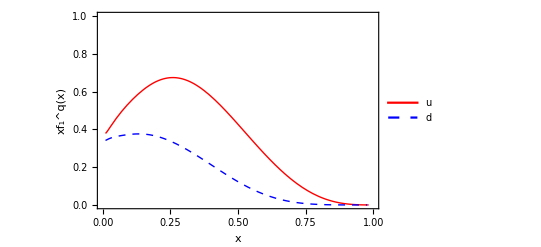

```mathematica
Plot[{x f1u[x,2.4],x f1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","xf_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
(*Eq. 5.1a  skip x in front of the structure function*)
avPT[z_]:= avp+avk z^2;

(* Call your functions with "nnpss" such that you can compare with functions available in the package*)

FUUnnpss[pion_,x_,z_,Q2_,PT_] := ((4.0/9.0)f1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sbar[x,Q2]D1sbar[pion,z,Q2])Exp[(-PT^2/avPT[z])]/(π avPT[z])
```

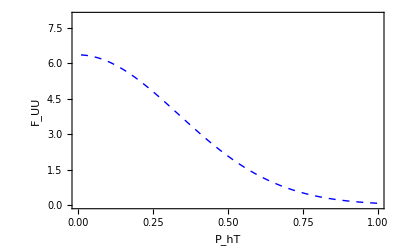

```mathematica
x=0.1;
z=0.3;
Q2=2.;

Plot[{FUU["pi+",x,z,Q2,PhT],FUUnnpss["pi+",x,z,Q2,PhT]},{PhT,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,8}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"P_hT","F_UU"},BaseStyle->{FontSize->12,FontFamily->"Arial"}]

Clear[x,z,Q2];
```

Phenomenology of leading twist double spin asymmetry A_LL

## F_LL analytical result:

```mathematica
Print["Eq(2.18 b)  C[g1 D1]"]
PTweightLL[pt_] := 1;
```

Eq(2.18 b)  C[g1 D1]

Eq(2.18 b)  C[g1 D1]

Eq(2.18 b)  C[g1 D1]

```mathematica
Print["Eq(2.18 b)   C[g1 D1]"]
ConvolutionTMD[omega0,g1,D1]
```

Eq(2.18 b)   C[g1 D1]

(D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1^2 z^2)) g_1)/(π p_TA^2+k_Tg1^2 π z^2)

```mathematica
Print["Eq(4.9) ∫ⅆ^2P_hT C[g1 D1]"]
PTConvolutionTMD[PTweightLL,omega0,g1,D1]
```

Eq(4.9) ∫ⅆ^2P_hT C[g1 D1]

D_1 g_1

## F_LL numerics:

```mathematica
avLLPT[z_]:= avp+avkg z^2;
(*Eq. 5.5a  skip x in front of structure functions*)
FLLnnpss[pion_,x_,z_,Q2_,PT_] := ((4.0/9.0)g1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1sbar[x,Q2] D1sbar[pion,z,Q2] ) Exp[(-PT^2/avLLPT[z])]/(π avLLPT[z])
```

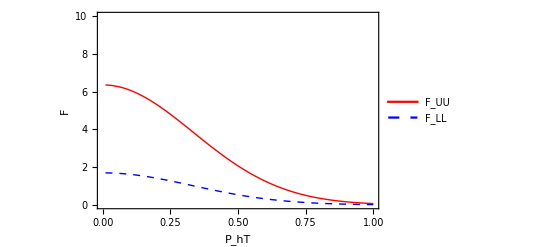

```mathematica
x=0.1;
z=0.3;
Q2=2.;

Plot[{FUUnnpss["pi+",x,z,Q2,PhT],FLLnnpss["pi+",x,z,Q2,PhT]},{PhT,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,10}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"P_hT","F"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"F_UU","F_LL"},{0.7,0.7}]]

Clear[x,z,Q2];
```

## A_LL numerics:

```mathematica
ALLnnpss[pion_,x_,z_,Q2_,PT_] := FLLnnpss[pion,x,z,Q2,PT]/FUUnnpss[pion,x,z,Q2,PT]  ;
```

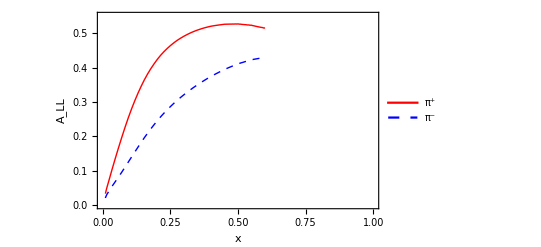

```mathematica
Plot[{ALLnnpss["pi+",x,0.34,2.4, 0.5],ALLnnpss["pi-",x,0.34,2.4, 0.5]},{x,0.01,0.6},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0.,0.55}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","A_LL"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.8,0.15}]]
```

Phenomenology of leading twist single spin asymmetry A_UT^sin[Φ_h-Φ_S]Sivers Asymmetry

## F_UT^sin[Φ_h-Φ_S] analytical result:

```mathematica
Print["Eq(2.18 d)   C[ -w_B^{1} f_(1  T)^perp D_1]"  ]
PTweightUTf1tperp[kt_] := 1;
```

Eq(2.18 d)   C[ -w_B^{1} f_(1  T)^perp D_1]

```mathematica
Print["Eq(2.18 d)  F_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ -w_B^{1} f_(1  T)^perp D_1] ="  ]
(* WRITE YOUR EXPRESSION HERE *)
-ConvolutionTMD[omega1B,f1Tperp,D1]
```

Eq(2.18 d)  F_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ -w_B^{1} f_(1  T)^perp D_1] =

-(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_TSIVERS^2 z^2)) f_T^(FIRST perp) M P_hT z)/(π (p_TA^2+k_TSIVERS^2 z^2)^2)

```mathematica
Print["Eq(2.18 d)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ -w_B^{1} f_(1  T)^perp D_1] ="  ]
```

Eq(2.18 d)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ -w_B^{1} f_(1  T)^perp D_1] =

## F_UT^sin[Φ_h-Φ_S] numerics:

```mathematica
(*Eq. 5.7a   *)
Mp=0.938;

(* WRITE YOUR EXPRESSION HERE *)

avUTPTf1tperp[z_]:= avp+avks z^2;  
FUTf1tperpnnpss[pion_,x_,z_,Q2_,PT_] := (-2z PT)((4.0/9.0)f1TperpuFirstMoment[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1TperpdFirstMoment[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1TperpsFirstMoment[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1TperpubarFirstMoment[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1TperpdbarFirstMoment[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1TperpsbarFirstMoment[x,Q2] D1sbar[pion,z,Q2] ) 1/(π avUTPTf1tperp[z]^2) Exp[(-PT^2/avUTPTf1tperp[z])]
```

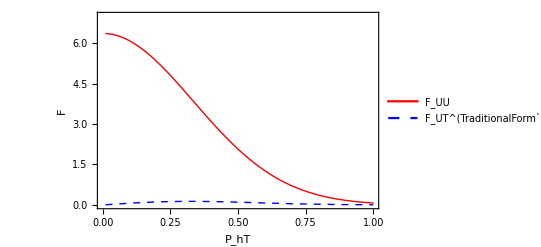

```mathematica
x=0.1;
z=0.3;
Q2=2.;

Plot[{FUUnnpss["pi+",x,z,Q2,PhT],FUTf1tperpnnpss["pi+",x,z,Q2,PhT]},{PhT,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,7}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"P_hT","F"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"F_UU","F_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},{0.7,0.7}]]

Clear[x,z,Q2];
```

## A_UT^sin[Φ_h-Φ_S]numerics:

```mathematica
AUTSiversnnpss[pion_,x_,z_,Q2_,PT_] := FUTf1tperpnnpss[pion,x,z,Q2,PT]/FUUnnpss[pion,x,z,Q2,PT];
```

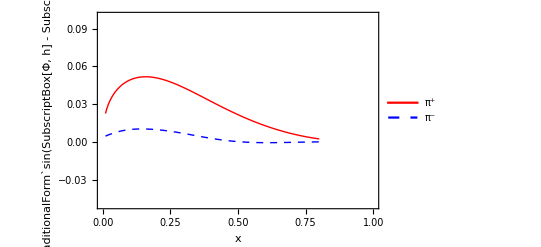

```mathematica
x=0.1;
z=0.3;
Q2=2.;
PT=0.5;
AUTSiverspipplot = Plot[{AUTSiversnnpss["pi+",x,z,Q2,PT] ,AUTSiversnnpss["pi-",x,z,Q2,PT] },{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.7}]]
Clear[x,z,Q2,PT]
```